```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
aDist=MultinormalDistribution[{0,0},{{1,0.95},{0.95,1}}];
lim=2;
```

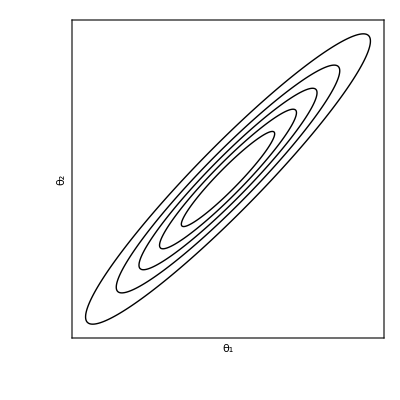

```mathematica
g1=Show[ContourPlot[PDF[aDist,{x,y}],{x,-lim,lim},{y,-lim,lim},ContourStyle->Black,ContourShading->None,Contours->5,FrameTicks->None,FrameLabel->{"θ_1","θ_2"},LabelStyle->{Black,FontSize->20},PlotRange->Full,PlotPoints->200]]
```

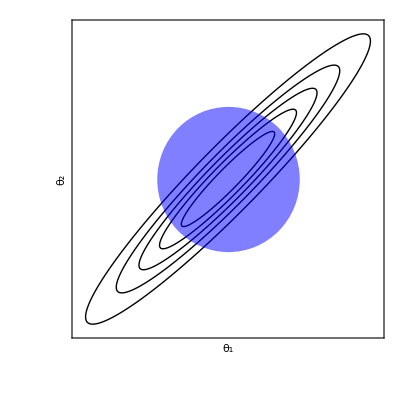

```mathematica
g2=Show[g1,Graphics[{Opacity[0.5,Blue],Ellipsoid[{0,0},{0.95,0.95}]}]]
```

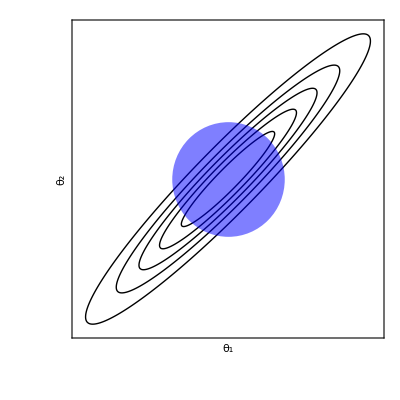

```mathematica
g3=Show[g1,Graphics[{Opacity[0.5,Blue],Ellipsoid[{0,0},{0.75,0.75}]}]]
```

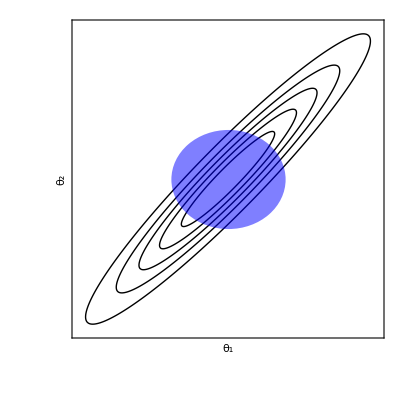

```mathematica
g4=Show[g1,Graphics[{Opacity[0.5,Blue],Ellipsoid[{0,0},{{0.5,0.2},{0.2,0.5}}]}]]
```

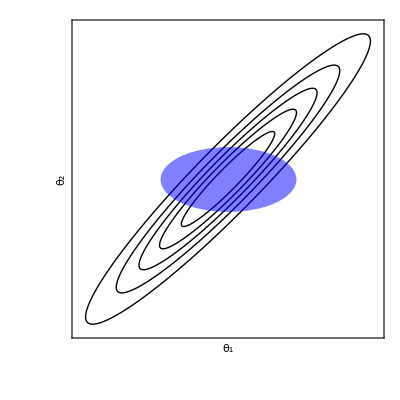

```mathematica
g5=Show[g1,Graphics[{Opacity[0.5,Blue],Ellipsoid[{0,0},{{0.5,0.4},{0.4,0.5}}]}]]
```

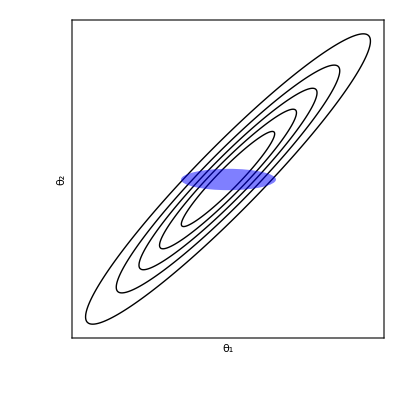

```mathematica
g6=Show[g1,Graphics[{Opacity[0.5,Blue],Ellipsoid[{0,0},{{0.21,0.2},{0.2,0.21}}]}]]
```

```mathematica
g={g1,g2,g3,g4,g5,g6};
```

```mathematica
ListAnimate[g]
```

```mathematica
Table[Export[StringJoin["adaptive_cartoon",ToString@i,".png"],g[[i]],ImageResolution->200],{i,1,Length@g,1}]
```

{adaptive_cartoon1.png,adaptive_cartoon2.png,adaptive_cartoon3.png,adaptive_cartoon4.png,adaptive_cartoon5.png,adaptive_cartoon6.png}